## 3^rd Order ΔΣM Block Diagram Reduction

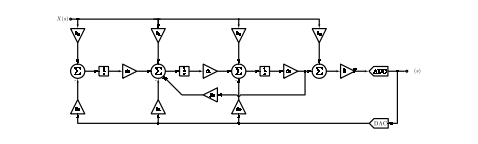

## Node Equations

Integrator 1 Output(scaled):

```mathematica
Subscript[γ, 1]=Subscript[c, 0]/s(Subscript[b, 0] X-Subscript[a, 0] Y);
```

Integrator 2 Output (scaled):

```mathematica
Subscript[γ, 2]=Subscript[γ, 2]/.Solve[Subscript[γ, 2]==Subscript[c, 1]/s(Subscript[γ, 1]+Subscript[b, 1] X-Subscript[a, 1] Y-Subscript[g, 0] Subscript[γ, 3]),Subscript[γ, 2]][[1]];
```

Integrator 3 Output (scaled):

```mathematica
Subscript[γ, 3]=Subscript[γ, 3]/.Solve[Subscript[γ, 3]==Subscript[c, 2]/s(Subscript[γ, 2]+Subscript[b, 2] X-Subscript[a, 2] Y),Subscript[γ, 3]][[1]];
```

Quantizer Input:

```mathematica
Subscript[γ, 4]=Subscript[γ, 4]/.Solve[Subscript[γ, 4]==k(Subscript[γ, 3]+Subscript[b, 3] X),Subscript[γ, 4]][[1]];
```

System Output:

```mathematica
Y=Y/.Solve[Y==Subscript[γ, 4]+Subscript[Err, ADC],Y][[1]]//FullSimplify;

Y=Collect[Collect[Expand[Numerator[Y]],Subscript[Err, ADC]],X]/Collect[Expand[Denominator[Y]],s];
```

## Transfer Functions

Cleanup :

```mathematica
Y=Y/.{k->1,Subscript[c, 0]->1,Subscript[c, 1]->1,Subscript[c, 2]->1};
```

```mathematica
STF=(Numerator[Y/.{Subscript[Err, ADC]->0}]/Denominator[Y])/X//Cancel; STF=Collect[Numerator[STF],s]/Collect[Denominator[STF],s]
```

(b_0+s^2 b_2+s^3 b_3+s (b_1+b_3 g_0))/(s^3+a_0+s^2 a_2+s (a_1+g_0))

```mathematica
NTF=(Numerator[Y/.{X->0}]/Denominator[Y])/Subscript[Err, ADC]//Cancel;NTF=Factor[Numerator[NTF]]/Collect[Denominator[STF],s]
```

(s (s^2+g_0))/(s^3+a_0+s^2 a_2+s (a_1+g_0))

## Solution

```mathematica
STFnum = CoefficientList[Numerator[STF],s];
Den = CoefficientList[Denominator[STF],s];
NTFnum = CoefficientList[Numerator[NTF],s];

FCoeff={Subscript[F, 3],Subscript[F, 2],Subscript[F, 1],Subscript[F, 0]};
MCoeff={Subscript[M, 3],Subscript[M, 2],Subscript[M, 1],Subscript[M, 0]};
GCoeff={Subscript[G, 3],Subscript[G, 2],Subscript[G, 1],Subscript[G, 0]};
```

```mathematica
Solve[
{
FCoeff[[1]]==STFnum[[1]],
FCoeff[[2]]==STFnum[[2]],
FCoeff[[3]]==STFnum[[3]],
FCoeff[[4]]==STFnum[[4]],
MCoeff[[1]]==Den[[1]],
MCoeff[[2]]==Den[[2]],
MCoeff[[3]]==Den[[3]],
MCoeff[[4]]==Den[[4]],
GCoeff[[1]]==NTFnum[[1]],
GCoeff[[2]]==NTFnum[[2]],
GCoeff[[3]]==NTFnum[[3]],
GCoeff[[4]]==NTFnum[[4]]
},
{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[b, 0],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}
]//Transpose//TableForm
```

a_0→M_3
a_1→-g_0+M_2
a_2→M_1
b_0→F_3
b_1→F_2-F_0 g_0
b_2→F_1
b_3→F_0